Lecture Notes on Condensed Matter Physics  | University of Tehran - Department Of Physics | Lecturer: Prf. Khazaei | Fall 2024 | Developed By: Amir H. Ebrahimnezhad

Amir H. Ebrahimnezhad

Physics Student At University of Tehran / Thisismeamir@outlook.com

The following notebook was generated based on the lectures of introduction to condensed matter physics at the university of Tehran. Feel free to get all of the notebooks at my GitHub repository 
( https://github.com/thisismeamir/condensedmatter-lecturenotes ).

# Crystal Structures

## An Introduction to Condensed Matter Physics

The goal of condensed matter physics is to understand how underlying laws unfold themselves in objects of the natural world. Because the complexity of condensed matter systems is so enormous, the number of atoms they involve so great, and the possibility of solving all underlying equations in full detail so remote, the laws of greatest importance are principles of symmetry.

## Crystals and Lattices

Definition: A Crystal is constructed by the infinite repetition of identical group of atoms. This group is called basis. This repetition can be thought of a transformation in space using a set of mathematical points to which the basis is attached. This set is called Lattice.

## Lattice

The lattice in three dimensions may be defined by three translation vectors (two for 2-dimensions and one for 1-dimensions as well), such that the arrangement of atoms in the crystal looks the same when viewed from the point r as when viewed from every other point

```mathematica
R[a1_,a2_, a3_]:= Module[{
u1,u2,u3},
a1 u1 + a2 u2 +a3 u3//MatrixForm
]
```

Primitive: The lattice is said to be primitive if any two points from which the atomic arrangement looks the same always satisfy the equation above with a suitable choice of the integers u_i. Using this we define the primitive translation vectors. There is no cell of smaller volume than

```mathematica
V[a1_?VectorQ,a2_?VectorQ,a3_?VectorQ]:= √Dot[a1, Cross[a2,a3]]
```

that can serve as a building block for the crystal structure. We often use these vectors to define the crystal axes, which form three adjacent edges of the primitive parallelepiped.

### A Visual Example: 2D Lattice

Let us begin by defining a function that given a list of basis, and an integer, draws the lattice shape for us.

```mathematica
Draw2DLattice[basis_List,n_Integer]:=Module[{latticePoints},(*Generate lattice points by creating all combinations of the basis vectors*)latticePoints=Flatten[Table[i*basis[[1]]+j*basis[[2]],{i,-n,n},{j,-n,n}],1];
Graphics[{Purple,PointSize[Medium],Point[latticePoints],(*Plot points*)Red,Thick,Arrow[{{0,0},#}]&/@basis,(*Draw lattice basis vectors*)Gray,Dashed,Line[{{-n*basis[[1]]-n*basis[[2]]},{n*basis[[1]]+n*basis[[2]]}}] (*Extend the axis lines*)},Axes->True,AxesOrigin->{0,0},Ticks->None]]
```

Now let’s define our basis vectors:

```mathematica
example2DLatticeVector1 = {1,0};
example2DLatticeVector2 = {1/2,√3/2};
```

This lattice would look like:

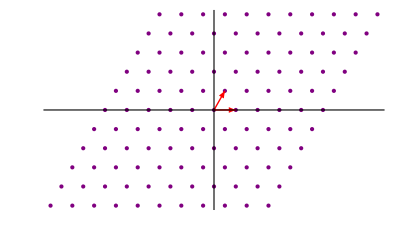

```mathematica
Draw2DLattice[{example2DLatticeVector1, example2DLatticeVector2}, 5]
```

But not every repetitive structure we see in nature can be described using lattice only. Since lattices are mathematical points, there is more variety to what is possible in crystals.

## Unit Cell

A unit cell is a region of space that, when repeated in all directions, can construct a complete periodic structure without leaving any gaps or causing overlaps. There are many possible choices of unit cells for a given structure, depending on how we define the boundaries. 

However, one particularly important type is the primitive unit cell.

Definition: A primitive unit cell is defined as the unit cell that has the minimum volume (in 3D), maximum area (in 2D), or minimum length (in 1D) among all possible unit cells. An alternative, yet equally valid, definition of a primitive unit cell is that it contains exactly one lattice point. The lattice points are the repeating points in space that define the crystal structure.

The vectors that span the primitive unit cell are called primitive lattice vectors, and the atoms associated with the primitive cell form a primitive basis.

To calculate whether a unit cell is primitive, we can use its lattice vectors to computed the following quantities (based on the dimension)

```mathematica
L[a_?VectorQ] := √(Dot[a,a]^2) (* Length: For 1 dimensional lattice *)
S[a1_?VectorQ, a2_?VectorQ] := √(Dot[a1,a2]^2) (* Surface Area: For 2 dimensional lattice *)
V[a1_?VectorQ, a2_?VectorQ, a3_?VectorQ]:=√Dot[a1, Cross[a2,a3]] 
(* Volume: For 3 dimensional lattice *)(*Yes I already defined the last one*)
```

If these are minimal, the unit cell is considered primitive. However, primitive unit cells are not necessarily unique. For some lattices, multiple primitive cells with the same volume or area can be found.

Additionally, a crystal can have various sets of primitive vectors, but the volume defined by these vectors remains constant. This property helps maintain the periodicity of the lattice, ensuring that different primitive unit cells of the same crystal describe the same structure.

Choosing the right unit cell: In practice, you often choose the one that remains invariant under the symmetries of the system you’re studying. This simplifies the analysis, especially for complex crystal structures.

### A Visual Example: Different primitive vectors result in the same lattice

Let’s begin this example by considering these two set of 2 dimensional vectors:

```mathematica
a1 = {1,0};
a2 = {1/2, √3/2};
b1 = {1,0};
b2 = -a2;
```

Now lets visualize them:

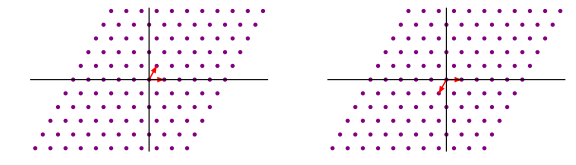

```mathematica
GraphicsRow[{Draw2DLattice[{a1,a2},5],Draw2DLattice[{b1,b2},5]},ImageSize->Large]
```

And now check if the surface area of these vectors match:

```mathematica
If[Equal[S[a1,a2],S[c1,c2]], Print["These two primitive cells have equal surface areas and thus both are acceptable!"]]
```

If[1/2==S[c1,c2],Print[These two primitive cells have equal surface areas and thus both are acceptable!]]

Wigner-Seitz Cell: Among the many ways to define a primitive cell, one well-known method is the Wigner-Seitz cell. It defines a region around a lattice point that is closer to that point than to any other lattice point. By repeating the Wigner-Seitz cell throughout space, one can fully cover the crystal structure.

The Wigner-Seitz construction gives an intuitive understanding of the local environment of a lattice point and is widely used in solid-state physics to study electronic properties of crystals.

### A Visual Example: A Simple 2D lattice with and without a unit cell.

First we define a function that would let us draw the structure given lattice basis and a set of unit cell:

```mathematica
(* This simply draws each point and unit cell *)
Draw2DLatticeWithUnitCell[basis_List,unitCell_List,n_Integer]:=Module[{latticePoints,allPoints},(*Generate lattice points*)latticePoints=Flatten[Table[i*basis[[1]]+j*basis[[2]],{i,-n,n},{j,-n,n}],1];
(*Generate all points including unit cell vectors*)allPoints=Flatten[Table[latticePoint+unitCellVector,{latticePoint,latticePoints},{unitCellVector,unitCell}],1];
Graphics[{(*Plot points*)Purple,PointSize[Medium],Point[allPoints],(*Draw lattice basis vectors*)Red,Thick,Arrow[{{0,0},#}]&/@basis,(*Draw unit cell vectors*)Blue,Thin,Arrow[{{0,0},#}]&/@unitCell,(*Extend the axis lines*)Gray,Dashed,Line[{{-n*basis[[1]]-n*basis[[2]]},{n*basis[[1]]+n*basis[[2]]}}]},Axes->True,AxesOrigin->{0,0},Ticks->None]]

(* This one let's you color the unit cells accordingly *)
Draw2DLatticeWithColoredUnitCell[basis_List,unitCellObj_,n_Integer]:=Module[{latticePoints,allPoints,allColors},(*Extract unit cell positions and colors*){unitCell,unitCellColors}={unitCellObj[[1]],unitCellObj[[2]]};
(*Generate lattice points*)latticePoints=Flatten[Table[i*basis[[1]]+j*basis[[2]],{i,-n,n},{j,-n,n}],1];
(*Generate all points including unit cell vectors*)allPoints=Flatten[Table[latticePoint+unitCellVector,{latticePoint,latticePoints},{unitCellVector,unitCell}],1];
(*Generate colors for all points*)allColors=Flatten[Table[color,{latticePoint,latticePoints},{color,unitCellColors}],1];
Graphics[{(*Plot colored points*)PointSize[Medium],MapThread[{#1,Point[#2]}&,{allColors,allPoints}],(*Draw lattice basis vectors*)Red,Thick,Arrow[{{0,0},#}]&/@basis,(*Draw unit cell vectors*)Blue,Thin,Arrow[{{0,0},#}]&/@unitCell,(*Extend the axis lines*)Gray,Dashed,Line[{{-n*basis[[1]]-n*basis[[2]]},{n*basis[[1]]+n*basis[[2]]}}]},Axes->True,AxesOrigin->{0,0},Ticks->None]]
```

Let’s define simple orthogonal lattice:

```mathematica
latticeBasis1 = {1,0};
latticeBasis2 = {0,1};
```

And a unit cell:

```mathematica
unitCell = {{1/4,√3/4},{1,0}};
```

Now we first draw our lattice to see it’s mathematical points structure:

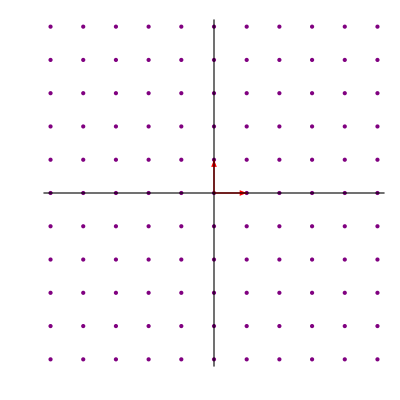

```mathematica
Draw2DLattice[{
latticeBasis1,
latticeBasis2
}, 5]
```

After this we add the unit cell:

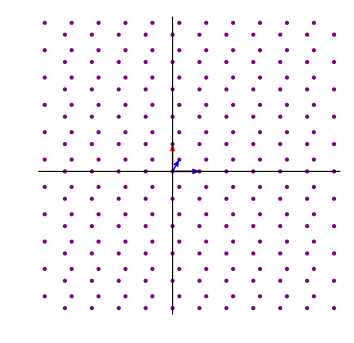

```mathematica
Draw2DLatticeWithUnitCell[{
latticeBasis1,
latticeBasis2
}, unitCell, 5]
```

We can also use the other function so that we have a bit of different colors to represent each point:

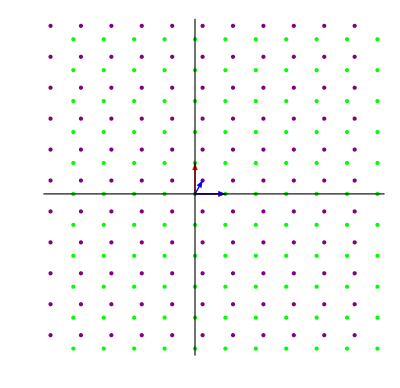

```mathematica
unitCell2D={unitCell,{Purple,Green}};
Draw2DLatticeWithColoredUnitCell[{latticeBasis1, latticeBasis2 },unitCell2D,5]
```

Overall we have

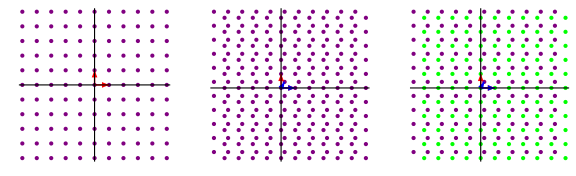

```mathematica
GraphicsRow[{Draw2DLattice[{latticeBasis1,latticeBasis2}, 5],
Draw2DLatticeWithUnitCell[{latticeBasis1,latticeBasis2}, unitCell, 5],
Draw2DLatticeWithColoredUnitCell[{latticeBasis1, latticeBasis2 },unitCell2D,5]}, ImageSize->Large
]
```

### A Visual Example: A 3D lattice with and without unit cells

Now let’s get things serious :) We would define these three functions that would let us draw a three dimensional structure given the lattice basis and the unit cells. The third one let’s us use coloring to get a better look:

```mathematica
Draw3DLattice[basis_List,n_Integer]:=Module[{latticePoints},(*Generate lattice points by creating all combinations of the basis vectors*)latticePoints=Flatten[Table[i*basis[[1]]+j*basis[[2]]+k*basis[[3]],{i,-n,n},{j,-n,n},{k,-n,n}],2];Graphics3D[{(*Plot points*){Purple,PointSize[Medium],Point[latticePoints]},(*Draw lattice basis vectors*){Red,Thick,Arrow[{{0,0,0},#}]&/@basis}},Boxed->False,Axes->True,AxesLabel->{"x","y","z"},ViewPoint->{2,-2,2},ViewVertical->{0,0,1}]] 
Draw3DLatticeWithUnitCell[basis_List,unitCell_List,n_Integer]:=Module[{latticePoints,allPoints},(*Generate lattice points*)latticePoints=Flatten[Table[i*basis[[1]]+j*basis[[2]]+k*basis[[3]],{i,-n,n},{j,-n,n},{k,-n,n}],2];
(*Generate all points including unit cell vectors*)allPoints=Flatten[Table[latticePoint+unitCellVector,{latticePoint,latticePoints},{unitCellVector,unitCell}],1];
Graphics3D[{(*Plot points*)Purple,PointSize[Medium],Point[allPoints],(*Draw lattice basis vectors*)Red,Thick,Arrow[{{0,0,0},#}]&/@basis,(*Draw unit cell vectors*)Blue,Thin,Arrow[{{0,0,0},#}]&/@unitCell},Boxed->False,Axes->True,AxesLabel->{"x","y","z"},ViewPoint->{2,-2,2},ViewVertical->{0,0,1},ImageSize->Large]]
Draw3DLatticeWithColoredUnitCell[basis_List,unitCellObj_,n_Integer]:=Module[{latticePoints,allPoints,allColors},(*Extract unit cell positions and colors*){unitCell,unitCellColors}={unitCellObj[[1]],unitCellObj[[2]]};
(*Generate lattice points*)latticePoints=Flatten[Table[i*basis[[1]]+j*basis[[2]]+k*basis[[3]],{i,-n,n},{j,-n,n},{k,-n,n}],2];
(*Generate all points including unit cell vectors*)allPoints=Flatten[Table[latticePoint+unitCellVector,{latticePoint,latticePoints},{unitCellVector,unitCell}],1];
(*Generate colors for all points*)allColors=Flatten[Table[color,{latticePoint,latticePoints},{color,unitCellColors}],1];
Graphics3D[{(*Plot colored points*)PointSize[Medium],MapThread[{#1,Point[#2]}&,{allColors,allPoints}],(*Draw lattice basis vectors*)Red,Thick,Arrow[{{0,0,0},#}]&/@basis,(*Draw unit cell vectors*)Blue,Thin,Arrow[{{0,0,0},#}]&/@unitCell},Boxed->False,Axes->True,AxesLabel->{"x","y","z"},ViewPoint->{2,-2,2},ViewVertical->{0,0,1}]]
```

Let’s begin by introducing the lattice:

```mathematica
latticeBasis3D1 = {1,0,0};
latticeBasis3D2 = {0,0,1};
latticeBasis3D3 = {0,1,0};
Draw3DLattice[{latticeBasis3D1, latticeBasis3D2, latticeBasis3D3}, 4]
```

-Graphics3D-

Now let’s add unit cells:

```mathematica
unitCell3D = {{0.5,0.5,0},{0.5,0,0.5},{0,0.5,0.5}};
Draw3DLatticeWithUnitCell[{latticeBasis3D1, latticeBasis3D2, latticeBasis3D3}, unitCell3D, 4]
```

-Graphics3D-

Now coloring it:

```mathematica
Draw3DLatticeWithColoredUnitCell[{latticeBasis3D1,latticeBasis3D2,latticeBasis3D3}, {unitCell3D,{Purple, Pink, Blue}}, 4]
```

-Graphics3D-